#### SG gain Lais DOPO WRONG

```mathematica
K = ({{-(1 + I Δ) - 4I a aconj, -2 I a^2}, {2 I aconj^2, -(1 - I Δ) + 4I a aconj}});
Eigenvalues[K]/.{a aconj->P, (a aconj)^2->P^2}
```

{ⅈ (ⅈ-√(12 P^2+8 P Δ+Δ^2)),ⅈ (ⅈ+√(12 P^2+8 P Δ+Δ^2))}

#### SG gain Lais DOPO

```mathematica
K = ({{-(1 + I Δ) + 4I a aconj, 2 I a^2}, {- 2 I aconj^2, -(1 - I Δ) - 4I a aconj}});
Eigenvalues[K]/.{a aconj->P, (a aconj)^2->P^2}
```

{ⅈ (ⅈ-√(12 P^2-8 P Δ+Δ^2)),ⅈ (ⅈ+√(12 P^2-8 P Δ+Δ^2))}

#### SG gain Paper OPO

```mathematica
K = ({{-(1 + I Δ) + 2I a aconj, I a^2}, {- I aconj^2, -(1 - I Δ) - 2I a aconj}});
Eigenvalues[K]/.{a aconj->P, (a aconj)^2->P^2}
```

{ⅈ (ⅈ-√(3 P^2-4 P Δ+Δ^2)),ⅈ (ⅈ+√(3 P^2-4 P Δ+Δ^2))}

#### Molecule gain

```mathematica
K=({{-(1+I Δ)+I (2 a aconj ), I a^2}, {- I aconj^2, -(1-I Δ)-I (2 a aconj )}});
```

```mathematica
Eigenvalues[K]/.{a aconj->P, (a aconj)^2->P^2}
```

{ⅈ (ⅈ-√(3 P^2-4 P Δ+Δ^2)),ⅈ (ⅈ+√(3 P^2-4 P Δ+Δ^2))}

#### General case

```mathematica
K=({{-(1+I Δ)+I (2 f1122 a aconj + 2 f3322 a aconj ), I 2 f1232 a^2}, {- I 2 f1232 aconj^2, -(1-I Δ)-I (2 f1122 a aconj + 2 f3322 a aconj  )}});
```

```mathematica
eigenvalues = Eigenvalues[K]/.{a aconj->P, (a aconj)^2->P^2}//Simplify
```

{-1-ⅈ √(4 f1122^2 P^2-4 f1232^2 P^2+4 f1122 P (2 f3322 P-Δ)+(-2 f3322 P+Δ)^2),-1+ⅈ √(4 f1122^2 P^2-4 f1232^2 P^2+4 f1122 P (2 f3322 P-Δ)+(-2 f3322 P+Δ)^2)}

```mathematica
eigenvalues/.{f1122->1, f3322->1, f1232->1}
```

{-1-ⅈ √(4 P (2 P-Δ)+(-2 P+Δ)^2),-1+ⅈ √(4 P (2 P-Δ)+(-2 P+Δ)^2)}

```mathematica
eigenvalues/.{f1122->1/2, f3322->1/2, f1232->1/2}
```

{-1-ⅈ √(2 P (P-Δ)+(-P+Δ)^2),-1+ⅈ √(2 P (P-Δ)+(-P+Δ)^2)}

```mathematica
4 f1122^2 P^2-4 f1232^2 P^2+4 f1122 P (2 f3322 P-Δ)+(-2 f3322 P+Δ)^2/.{f1122->A0, f3322->B0, f1232->C0}//Simplify
```

4 A0^2 P^2-4 C0^2 P^2+4 A0 P (2 B0 P-Δ)+(-2 B0 P+Δ)^2

```mathematica
G =-(-4 C0^2 P^2 + (-2 (A0+B0) P+Δ)^2)/.{A0->f1122, B0->f3322, C0->f1232}
```

4 f1232^2 P^2-(-2 (f1122+f3322) P+Δ)^2

```mathematica
g = -1 + √G
```

-1+√(4 f1232^2 P^2-(-2 (f1122+f3322) P+Δ)^2)

```mathematica
g/.{f1122->1, f3322->1, f1232->1}
```

-1+√(4 P^2-(-4 P+Δ)^2)

```mathematica
g/.{f1122->1/2, f3322->1/2, f1232->1/2}
```

-1+√(P^2-(-2 P+Δ)^2)

#### Plots

```mathematica
gSG[P_, Δ_, D2_, κ_]:= -1 + √(4 P^2 - (1/κ(Δ + D2/2) - 4 P)^2)

gPM[P_, Δ_, J2_, κ_]:= -1 + √(P^2 - (1/κ(Δ + J2/2 )- 2 P)^2)
```

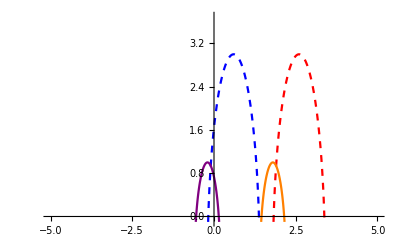

```mathematica
rnum = {P->2, κ->.2, GVD->2};
plt1 = Plot[gSG[P, Δ, -GVD, κ]/.rnum,{Δ,-5,5}, PlotRange->{{-5,5}, {-.1, 3.7}},PlotStyle->{Dashed, Red}];
plt2 = Plot[gSG[P, Δ, GVD, κ]/.rnum,{Δ,-5,5}, PlotRange->{{-5,5}, {-.1, 3.7}},PlotStyle->{Dashed, Blue}];
plt3 =Plot[gPM[P, Δ, -GVD, κ]/.rnum,{Δ,-5,5}, PlotRange->{{-5,5}, {-.1, 3.7}},PlotStyle->Orange];
plt4 =Plot[gPM[P, Δ, GVD, κ]/.rnum,{Δ,-5,5}, PlotRange->{{-5,5}, {-.1, 3.7}},PlotStyle->Purple];
Show[plt1,plt2, plt3, plt4]
```

```mathematica
Manipulate[Plot[{gSG[P, Δ, -GVD, κ],gSG[P, Δ, GVD, κ],gPM[P, Δ, -GVD, κ],gPM[P, Δ, GVD, κ]},{Δ,-5,5}, PlotRange->{{-5,5}, {-.1, 3.7}}, PlotStyle->{{Dashed, Red},{Dashed, Blue},{Orange},{Purple}}],{P,0,5},{GVD,0,5},{κ,0.1,2}]
```